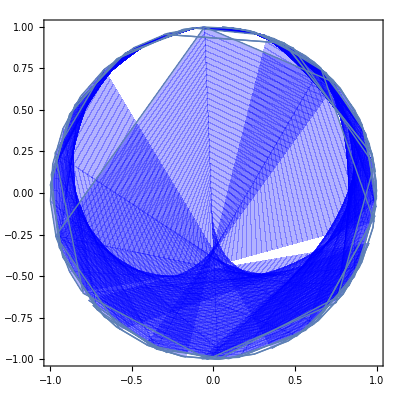

```mathematica
ClearAll["Global`*"];
r[t_]:=(x=-Sin[t];y=Cos[t];{x,y});
f[n_]:=n*4;
g[n_]:=n/2^Floor[Log[n]];
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1},PlotStyle->Blue]
```

```mathematica
f[n_]:=n*4;
δ=0.01;
trg[x_]:=1-2 ArcCos[(1-δ) Sin[2 π x]]/π;
sqr[x_]:=2 ArcTan[Sin[2 π x]/δ]/π;
swt[x_]:=(1+trg[(2 x-1)/4] sqr[x/2])/2;
flr[x_]:=x-swt[x]
g[n_]:=n/2^((Log[n]-SawtoothWave[Log[n]]));
parametricFunc[t_,u_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];{P1[[1]]+u*(P2[[1]]-P1[[1]]),P1[[2]]+u*(P2[[2]]-P1[[2]])});
ParametricPlot[parametricFunc[t,u],{t,0.01,1},{u,0,1},PlotStyle->Blue]

h[x_,y_,t_]:=(P1=r[2Pi*g[t]];P2=r[2Pi*g[f[t]]];(y-P1[[2]])*(P2[[1]]-P1[[1]])-(x-P1[[1]])*(P2[[2]]-P1[[2]]));
hd[t_]:=D[h[x_,y_,t],t];
Print[hd[t_]];
Print[FullSimplify[hd[t_]]];
```

-Graphics-

-2^(1-Log[t_]+SawtoothWave[Log[t_]]) π Cos[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_] (-Cos[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_]+Cos[2^(3-Log[4 t_]+SawtoothWave[Log[4 t_]]) π t_])+(2^(1-Log[t_]+SawtoothWave[Log[t_]]) π Cos[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_]-2^(3-Log[4 t_]+SawtoothWave[Log[4 t_]]) π Cos[2^(3-Log[4 t_]+SawtoothWave[Log[4 t_]]) π t_]) (-Cos[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_]+y_)+2^(1-Log[t_]+SawtoothWave[Log[t_]]) π Sin[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_] (Sin[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_]-Sin[2^(3-Log[4 t_]+SawtoothWave[Log[4 t_]]) π t_])-(x_+Sin[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_]) (2^(1-Log[t_]+SawtoothWave[Log[t_]]) π Sin[2^(1-Log[t_]+SawtoothWave[Log[t_]]) π t_]-2^(3-Log[4 t_]+SawtoothWave[Log[4 t_]]) π Sin[2^(3-Log[4 t_]+SawtoothWave[Log[4 t_]]) π t_])

2 π (-2^(-Floor[Log[t_]]) (Cos[2 (2^(-Floor[Log[t_]])-2^(2-Floor[Log[4 t_]])) π t_]-Cos[2^(1-Floor[Log[t_]]) π t_] y_+x_ Sin[2^(1-Floor[Log[t_]]) π t_])+2^(2-Floor[Log[4 t_]]) (Cos[2 (2^(-Floor[Log[t_]])-2^(2-Floor[Log[4 t_]])) π t_]-Cos[2^(3-Floor[Log[4 t_]]) π t_] y_+x_ Sin[2^(3-Floor[Log[4 t_]]) π t_]))